```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
```

plot2Doption

importData

jsonInfo

```mathematica
surgeExp=Import[FileNameJoin[{NotebookDirectory[],"surge.csv"}]];
tensionExp=Import[FileNameJoin[{NotebookDirectory[],"tension1.csv"}]];
heaveExp=Import[FileNameJoin[{NotebookDirectory[],"heave.csv"}]];
pitchExp=Import[FileNameJoin[{NotebookDirectory[],"pitch.csv"}]];
```

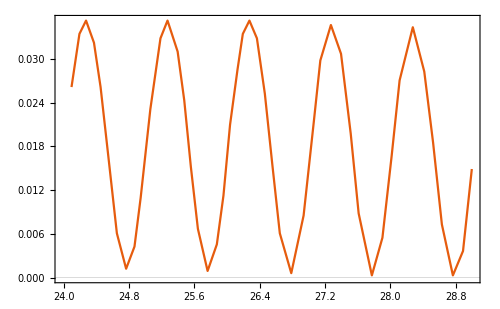

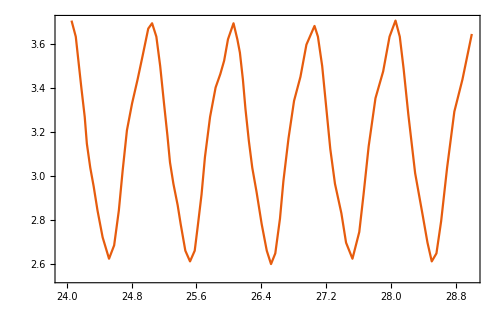

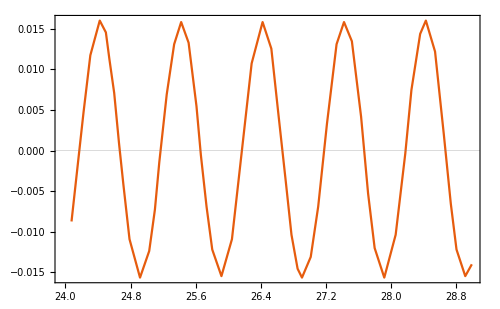

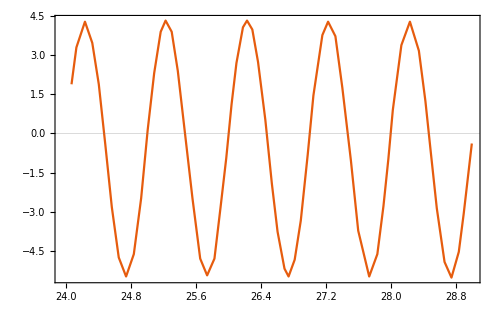

```mathematica
ListPlot[surgeExp,Joined->True,Evaluate[plot2Doption]]
ListPlot[tensionExp,Joined->True,Evaluate[plot2Doption]]
ListPlot[heaveExp,Joined->True,Evaluate[plot2Doption]]
ListPlot[pitchExp,Joined->True,Evaluate[plot2Doption]]
```

/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json

no. | title | length
1 | cpu_time | 1110
2 | float_COM | 1110
3 | float_EK | 1110
4 | float_EP | 1110
5 | float_accel | 1110
6 | float_area | 1110
7 | float_force | 1110
8 | float_pitch | 1110
9 | float_roll | 1110
10 | float_torque | 1110
11 | float_velocity | 1110
12 | float_yaw | 1110
13 | simulation_time | 1110
14 | wall_clock_time | 1110
15 | water_E | 1110
16 | water_EK | 1110
17 | water_EP | 1110
18 | water_face_size | 1110
19 | water_point_size | 1110
20 | water_volume | 1110

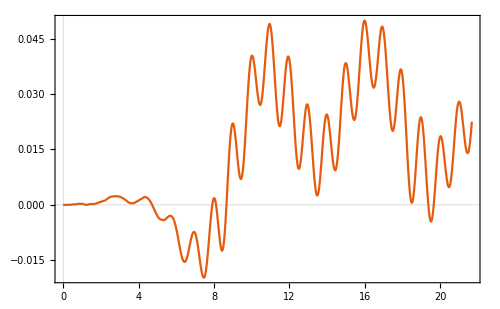

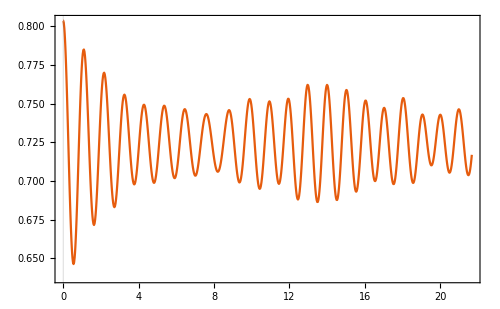

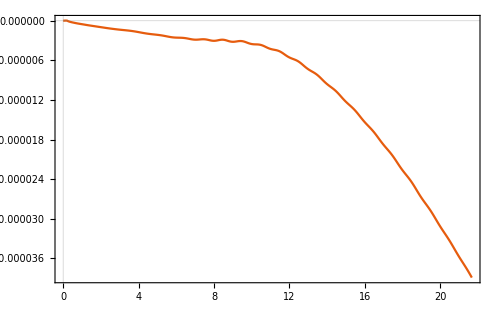

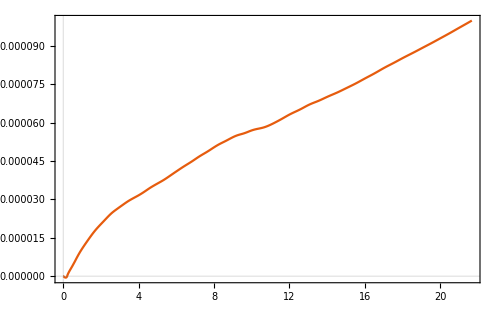

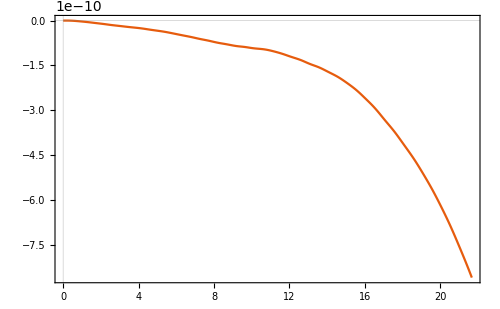

```mathematica
nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json"
jsonInfo[nameSim]

time=importData[nameSim,"simulation_time"];
surgeSim=importData[nameSim,"float_COM",1]-6;
heaveSim=importData[nameSim,"float_COM",3];
forceSim=importData[nameSim,"float_force"];
pitchSim=importData[nameSim,"float_pitch"];
rollSim=importData[nameSim,"float_roll"];
yawSim=importData[nameSim,"float_yaw"];
torqueSim=importData[nameSim,"float_torque"];

ListPlot[Transpose@{time,surgeSim},Joined->True,Evaluate[plot2Doption]]
ListPlot[Transpose@{time,heaveSim},Joined->True,Evaluate[plot2Doption]]
ListPlot[Transpose@{time,pitchSim},Joined->True,Evaluate[plot2Doption]]
ListPlot[Transpose@{time,rollSim},Joined->True,Evaluate[plot2Doption]]
ListPlot[Transpose@{time,yawSim},Joined->True,Evaluate[plot2Doption]]
```